```mathematica
ggx[θ_,α_]:=α^2/(π(Cos[θ]^2(α^2-1)+1)^2)
(* change[] gives cos(Subscript[θ, h]) when provided with Subscript[ω, i] and Subscript[ω, o] *)
change[θo_,θi_,ϕi_]:=(Cos[θo]+Cos[θi])/(√(2*(1+Cos[θo]*Cos[θi]+Sin[θo]*Sin[θi]*Sin[ϕi])))
E0[θo_,α_]:=Integrate[Integrate[ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2}],{ϕi,-π,π}]
```

Let’s test our formulas:

```mathematica
Plot3D[ggx[x,y],{x,0,π/2},{y,0.001,1}]
```

-Graphics3D-

```mathematica
Manipulate[2π*Integrate[ggx[θ,α]*Cos[θ]*Sin[θ],{θ,0,π/2}],{α,0.001,1}]
change[0,π/2,0]
```

1/(√2)

```mathematica
E0[0,0.5]
```

$Aborted

### C# Simulation

```mathematica
SetDirectory[NotebookDirectory[]]; 
countX = 128;
countY= 128;
rawFile=BinaryReadList["MSBRDF_E"<>ToString[countX]<>"x"<>ToString[countY]<>".float", "Real32"];
E0=Table[{Mod[i,countX]/(countX-1),Quotient[i,countX]/(countY-1), rawFile[[1+i]]},{i,0,countX*countY-1}];
```

```mathematica
ListPlot3D[E0,PlotRange->{0,1},AxesLabel->{"cos(θ)","α"}]
```

-Graphics3D-

```mathematica
Image[Table[Table[1-E0[[1+countX*y+x]][[3]],{x,0,countX-1}],{y,0,countY-1}]]
```

-Graphics-

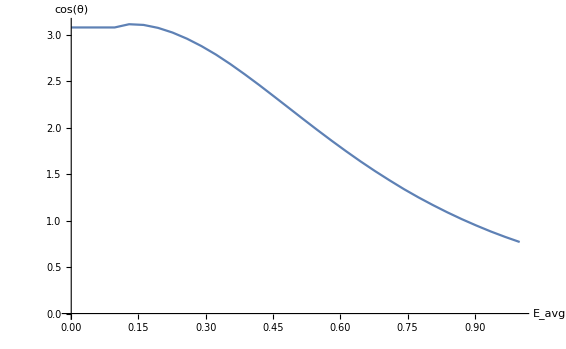

```mathematica
countX=32;
rawFileAvg=BinaryReadList["MSBRDF_Eavg32.float", "Real32"];
Eavg=Table[{Mod[i,countX]/(countX-1),rawFileAvg[[1+i]]},{i,0,countX-1}];
ListLinePlot[Eavg,AxesLabel->{"cos(θ)","E_avg"}]
```